将 MagneticTB 能带拟合到 VASP

要用 VASP 能带拟合紧束缚模型，先读取 EIGENVAL，再根据对称性构造 Hamiltonian。下面用三轨道模型拟合三条能带，比较最近邻和第二近邻的结果，再介绍只拟合某个能量范围或 k 点附近的用法。把拟合能带和 VASP 能带画在一起，就可以看出哪些地方符合、哪些地方还有差别。

```mathematica
Needs["MagneticTB`"]
```

读取并检查三条 VASP 能带

用 vaspEig 读取第 21 至 23 条能带，并减去费米能级。先把三条带都画出来，查看要拟合的能带：

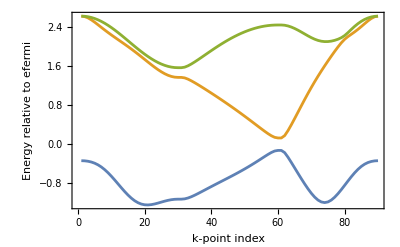

```mathematica
eigenvalFile = FileNameJoin[{
  NotebookDirectory[],
  "..", "ReferencePages", "Symbols", "EIGENVAL"
}];
vaspBands = vaspEig[eigenvalFile, -0.0072, 1, 21, 23];
ListLinePlot[
  Transpose[vaspBands[[All, 2]]],
  Frame -> True,
  FrameLabel -> {"k-point index", "Energy relative to efermi"},
  PlotRange -> All
]
```

构造对称性生成的模型

这里的三轨道模型使用 msgop[gray[156]] 的前六个操作，它们组成完整的幺正子群。onsite 和最近邻项含有 e1、e2 以及 t1 至 t9，这些就是需要拟合的参数：

```mathematica
init[
  lattice -> {
    {a, 0, 0},
    {-a/2, Sqrt[3] a/2, 0},
    {0, 0, c}
  },
  lattpar -> {a -> 1, c -> 10},
  wyckoffposition -> {{{2/3, 1/3, 0}, {0, 0, 0}}},
  symminformation -> Take[msgop[gray[156]], 6],
  basisFunctions -> {{"dz2", "dxy", "dx2-y2"}},
  InitialBondShells -> 3
];
fittingHamiltonian = symham[1] + symham[2];
fittingPath = {
  {{{0, 0, 0}, {1/2, 0, 0}}, {"Γ", "M"}},
  {{{1/2, 0, 0}, {1/3, 1/3, 0}}, {"M", "K"}},
  {{{1/3, 1/3, 0}, {0, 0, 0}}, {"K", "Γ"}}
};
initialRules = {
  e1 -> 0.915, e2 -> 0.685,
  t1 -> 0.1, t2 -> 0.09, t3 -> 0.1,
  t4 -> -0.38, t5 -> 0.34, t6 -> 0.245,
  t7 -> 0.565, t8 -> 0.305, t9 -> 0.365
};
```

拟合 onsite 与最近邻模型

先拟合全部 90 个 k 点处的三条能带，再与 VASP 能带画在同一张图上：

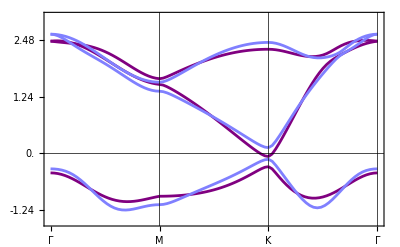
-Graphics-Purple: TB, Blue: VASP

```mathematica
nearestFit = fittingTB[
  fittingHamiltonian, vaspBands,
  Range[Length[vaspBands]], initialRules
];
compareBand[
  fittingPath, 30, fittingHamiltonian,
  nearestFit["FittedParams"], vaspBands,
  plotRange -> {-1.5, 3}
]
```

加入第二近邻 hopping

加入第二近邻时，用刚才得到的最近邻参数作为初值，新增的 r1 至 r10 先设为零。再拟合一次，对比两张能带图，就可以看出第二近邻跃迁改善了哪些部分。

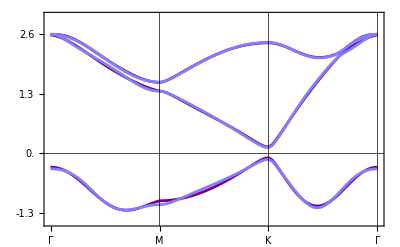
-Graphics-Purple: TB, Blue: VASP

```mathematica
secondNeighborHamiltonian = fittingHamiltonian + symham[3];
secondNeighborInitialRules = Join[
  nearestFit["FittedParams"],
  Thread[{r1, r2, r3, r4, r5, r6, r7, r8, r9, r10} -> 0.]
];
secondNeighborFit = fittingTB[
  secondNeighborHamiltonian, vaspBands,
  Range[Length[vaspBands]], secondNeighborInitialRules
];
compareBand[
  fittingPath, 30, secondNeighborHamiltonian,
  secondNeighborFit["FittedParams"], vaspBands,
  plotRange -> {-1.5, 3}
]
```

只拟合关心的能量范围

如果只关心费米能级附近的能带，可以用 EnergyWindow 指定能量范围，拟合时只计入这个范围内的参考能量。图中仍画出完整能带，便于同时查看范围以外的变化。

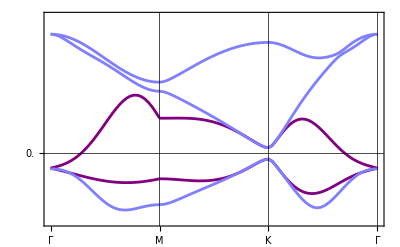
-Graphics-Purple: TB, Blue: VASP

```mathematica
fermiFit = fittingTB[
  fittingHamiltonian, vaspBands,
  Range[Length[vaspBands]], initialRules,
  "EnergyWindow" -> {-0.5, 0.5}
];
compareBand[
  fittingPath, 30, fittingHamiltonian,
  fermiFit["FittedParams"], vaspBands,
  plotRange -> {-1.5, 3}
]
```

只拟合 K 点附近

如果只拟合 K 点附近，可以用 KPointNeighborhood 指定 K 点和半径 0.15。这里采用倒空间分数坐标，距离计算考虑 k 点的周期等价位置。ComparisonPlot 只显示这个范围：蓝点是 VASP 能带，灰色虚线是初始模型，红线是拟合结果。

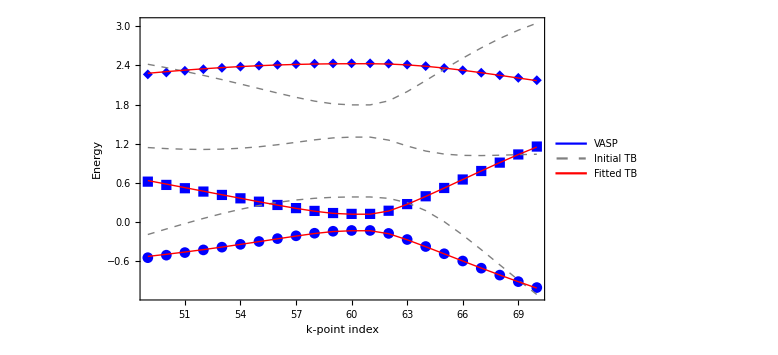

```mathematica
kFit = fittingTB[
  fittingHamiltonian, vaspBands,
  Range[Length[vaspBands]], initialRules,
  "KPointNeighborhood" -> <|
    "Center" -> {1/3, 1/3, 0},
    "Radius" -> 0.15,
    "Periodic" -> True
  |>
];
kFit["ComparisonPlot"]
```

根据能带图判断，不要只看损失

fittingTB 比较排序后的模型本征值与对应的参考能量，并不额外约束带隙，也不追踪轨道成分和能带连接关系。因此，数值误差小还不够，还要看图中的带隙和交叉是否正确。初值应有合理的物理依据；增加更远的近邻跃迁时，可以沿用已有的拟合参数。

相关函数

vaspEig   bandManipulateEig   fittingTB   compareBand

MagneticTB 帮助主页

MagneticTB

历史